# Support Vector Machine

Yang Long

#### Sigmoid Function

g(z)=1/(1+e^-z)

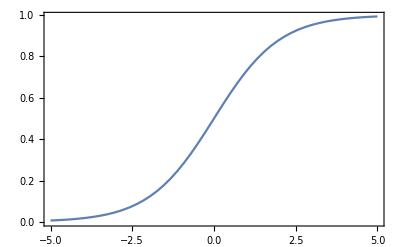

```mathematica
Plot[1/(1+Exp[-z]),{z,-5,5},Axes->False,Frame->True]
```

#### Logistic Classification

h_θ(x)=g(θ^T x)=1/(1+e^(-θ^Tx))

P(y=1|x,θ)=h_θ(x)
P(y=0|x,θ)=1-h_θ(x)

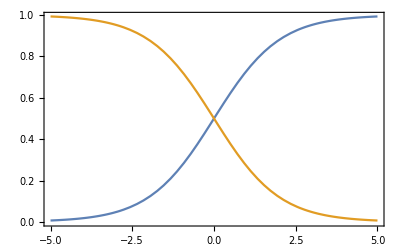

```mathematica
Plot[{1/(1+Exp[-x]),1-1/(1+Exp[-x])},{x,-5,5},Axes->False,Frame->True]
```

#### Margin

Super Plane:  y=f(x)=ω^T x+b

##### Functional Margin

γ̂=y(ω^T x+b)=y f(x)

γ̂= min (γ̂)_i (i=1,...,n)

##### Geometrical Margin

For point x, γ

x=x_0+γ ω/(||ω||)

So as to f((x⃗)_0)=0, we have

f(x)=f(x_0+γ  ω/(||ω||))=ω^T x_0+γ(ω^T ω)/(||ω||)+b=γ(ω^T ω)/(||ω||)=γ ||ω||

γ=(f(x))/(||ω||)=(ω^T x+b)/(||ω||)

The geometrical margin:

γ̃=y γ=y(ω^T x+b)/(||ω||)=(γ̂)/(||ω||)

#### Maximum Margin Classifier

max γ̃

y_i(ω^T x_i+b)=(γ̂)_i≥ γ̂, i=1,...,n

Set γ̂=1, minimize functional margin firstly, and then maximize geometrical margin.  So we have

max 1/(||ω||), s.t. y_i(ω^T x_i+b)≥ 1,i=1,...,n

#### Form conversion

SVM eigenequation

max 1/(||ω||)   s.t., y_i(ω^T x_i+b)≥ 1, i=1,..., n

min 1/2||ω(||)^2 s.t. y_i(ω^T x_i+b)≥ 1, i=1,...,n

To minimize 1/2||ω(||)^2 with the linear restricted conditions is a classical Quadratic programming (QP).

#### Lagrange Multiplier

L(ω,b,α)=1/2||ω(||)^2-(∑_(i=1))^n α_i(y_i(ω^T x_i+b)-1)

θ(ω)=max_(α_i≥ 0) L(ω,b,α)

min_(ω,b) θ(ω)=min_(ω,b) max_(α_i≥ 0) L(ω,b,α)=p^*

max_(α_i≥ 0) min_(ω,b) L(ω,b,α)=d^*

d^*≤ p^*

so max_(α_i≥ 0) min_(ω,b) L(ω,b,α) will be the new eigenequation. (1)Minimize L by ω, b firstly; (2)Maximize L by α.

#### KKT

#### SMO

#### Linearly Un-Separable

#### Kernel

#### Outliers